# comparison-2

## initial

```mathematica
result`dir=FileNameJoin[{NotebookDirectory[],"/expression-results/"}]
```

C:\octet.formfactor\expression-results

## import interpolate functions

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

C:\octet.formfactor\expression-fig

```mathematica
Once[fun`interp`calc`baryons`gegm`total=Get[FileNameJoin[{directory`fig,
"fun`interp`calc`baryons`gegm`total`L-0.90`ci-1.5.m"
}]]];
```

Interpolation::inddp: 维度 1 中的点 2.04082×10^-8 是重复的.

General::stop: 在本次计算中，Interpolation::inddp 的进一步输出将被抑制.

## import radius

导入半径信息

```mathematica
Once[rearrange`radius2`gegm`seva=Get[FileNameJoin[{result`dir,
"rearrange`radius2`gegm`seva`gegm.total`L-0.90`ci-1.5.m"
}]]];
```

```mathematica
rearrange`radius2`gegm`seva//Dimensions
```

{2,9,8}

rearrange`radius2`gegm`seva,{2,9,8},{gegm,config,io}

(*1;"tree", all*)(*2;"tree", u*)(*3;"tree", d*)(*4;"tree", s*)
(*5;"loop", all*)(*6;"loop", u*)(*7;"loop", d*)(*8;"loop", s*)
(*9"all", all*)

```mathematica
gegm=1;seva=5;io=2;
rearrange`radius2`gegm`seva⟦gegm,seva,io⟧
```

{0.016075,-0.0597245,0.00178607,0.0344576,0.0275938,-0.0334922,0.134263,0.0123744,0.00871777,-0.0670733,-0.0255806}

## ge

## Σ0

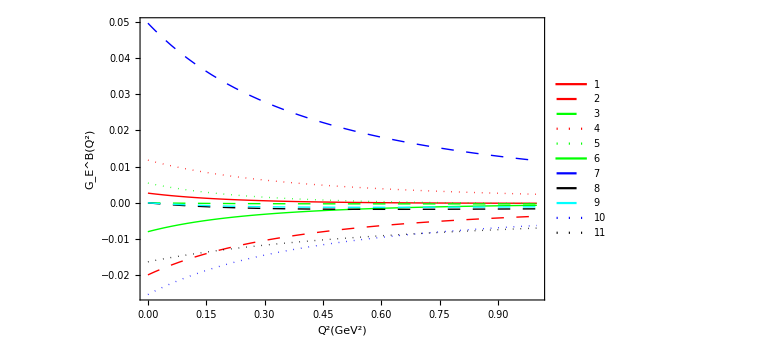

```mathematica
{{1, 0.012454482447554595}, {2, -0.06096906113729004}, {3, 0.00272037557420642}, {4, 0.03445755816086344}, {5, 0.02102850302361612}, {6, -0.043493753945467534}, {7, 0.1528897722953536}, {8, 0.000049478066089265994}, {9, -0.016373589906669178}, {10, -0.07410218663635183}, {11, -0.04580724424366759}}
```

## 7

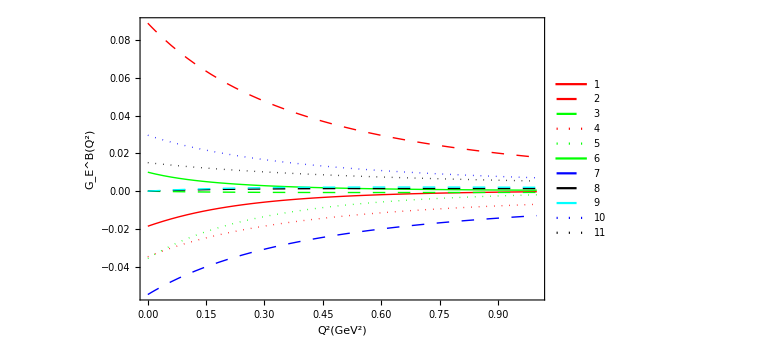

```mathematica
{{1, -0.07783160966666129}, {2, 0.2826279150165591}, {3, 0.008574751829239684}, {4, -0.10151170296690325}, {5, -0.13655043231956673}, {6, 0.08935344998904149}, {7, -0.16203713695731098}, {8, -0.0009294987944867883}, {9, 0.021942344753963505}, {10, 0.08652204307443247}, {11, 0.061927146288586685}}
```

## gm

```mathematica
octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613}
```

## Σ0

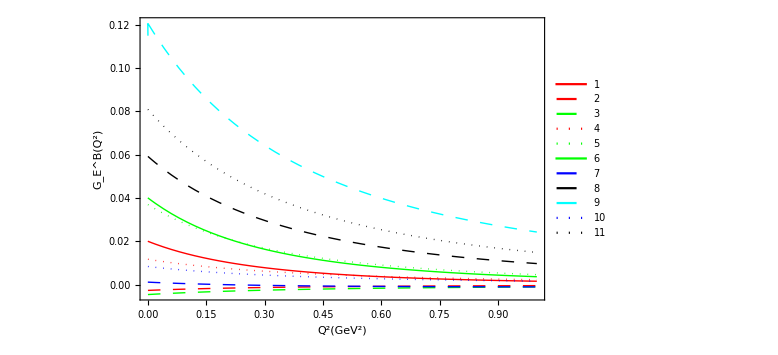

```mathematica
{{1, 0.028529650542906976}, {2, -0.002950955399369052}, {3, -0.003913334510190883}, {4, 0.01163591959132557}, {5, 0.0445396017158639}, {6, 0.05471084100553422}, {7, 0.0034911681946772615}, {8, 0.059398255646717545}, {9, 0.11901272019161153}, {10, 0.008341150981705004}, {11, 0.08267408577755173}}
```

## derivative comparison

```mathematica
gegm=1;config=1;io=2;if=Span[1,11];treeloop=2;seva=5;
zero`limit=0.00033;
Through[fun`interp`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧[zero`limit]]
Grid[
Transpose[
{
Range[0,11,1],
Prepend[
(-6)*(0.197326)*
Through[(Derivative[1]/@fun`interp`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧)[zero`limit]],
"from curve"
],
Prepend[
rearrange`radius2`gegm`seva⟦gegm,seva,io,if⟧,
"calced"
]
}
],
Frame->All
]
```

{0.00267407,-0.0199044,-4.97423×10^-7,0.0117774,0.0054478,-0.00797458,0.0495981,-3.446×10^-6,-2.69819×10^-6,-0.0253297,-0.0162961}

0 | from curve | calced
1 | 0.0160469 | 0.016075
2 | -0.0596507 | -0.0597245
3 | 0.00178318 | 0.00178607
4 | 0.0344155 | 0.0344576
5 | 0.0275509 | 0.0275938
6 | -0.0334827 | -0.0334922
7 | 0.134104 | 0.134263
8 | 0.0123523 | 0.0123744
9 | 0.00817636 | 0.00871777
10 | -0.0669943 | -0.0670733
11 | -0.0255582 | -0.0255806